```mathematica
Array[f, 24]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],f[11],f[12],f[13],f[14],f[15],f[16],f[17],f[18],f[19],f[20],f[21],f[22],f[23],f[24]}

```mathematica
f[1]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-350.0-500.0"];
f[2]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-500.0-645.0"];
f[3]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-657.0-691.0"];
f[4]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-710.0-715.0"];
f[5]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-740.0-759.0"];
f[6]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-767.0-810.0"];
f[7]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-844.0-890.0"];
f[8]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-350.0-500.0"];
f[9]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-500.0-645.0"];
f[10]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-657.0-691.0"];
f[11]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-710.0-715.0"];
f[12]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-740.0-759.0"];
f[13]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-767.0-810.0"];
f[14]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-844.0-890.0"];
f[15]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-350.0-500.0"];
f[16]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-500.0-645.0"];
f[17]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-657.0-691.0"];
f[18]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-710.0-715.0"];
f[19]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-740.0-759.0"];
f[20]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-767.0-810.0"];
f[21]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-844.0-890.0"];
```

```mathematica
f[22]=Import["/home/f10/r1xu/Summer_Research/2010/C2010-188-1051-350.0-890.0"];
f[23]=Import["/home/f10/r1xu/Summer_Research/2010/C2010-200-1312-350.0-890.0"];
f[24]=Import["/home/f10/r1xu/Summer_Research/2010/C2010-208-1328-350.0-890.0"];
```

```mathematica
Array[n, 24]
```

{n[1],n[2],n[3],n[4],n[5],n[6],n[7],n[8],n[9],n[10],n[11],n[12],n[13],n[14],n[15],n[16],n[17],n[18],n[19],n[20],n[21],n[22],n[23],n[24]}

```mathematica
i=1; While[i<25, n[i]=NonlinearModelFit[f[i], a x^b, {a, b}, x, MaxIterations-> 100000]; i++]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
Show[ListPlot[f[1]], Plot[n[1][x], {x, 350,500}]]     n[1]
```

```mathematica
Array[p, 24]
```

{p[1],p[2],p[3],p[4],p[5],p[6],p[7],p[8],p[9],p[10],p[11],p[12],p[13],p[14],p[15],p[16],p[17],p[18],p[19],p[20],p[21],p[22],p[23],p[24]}

```mathematica
j=1; While[j<25, p[j]=n[j]["ParameterConfidenceIntervalTable"]; j++]
```

```mathematica
p[1]
```

| Estimate | Standard Error | Confidence Interval
a | 14.3612 | 10.3287 | {-5.96496,34.6873}
b | -0.641363 | 0.119192 | {-0.875925,-0.406801}

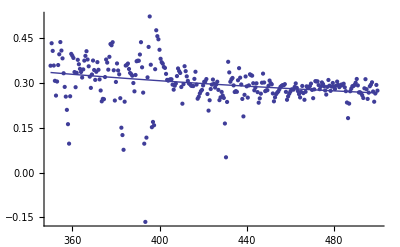

```mathematica
Show[ListPlot[f[1]], Plot[n[1][x], {x, 350, 500}]]
```

```mathematica
p[1]
```

| Estimate | Standard Error | Confidence Interval
a | 14.3612 | 10.3287 | {-5.96496,34.6873}
b | -0.641363 | 0.119192 | {-0.875925,-0.406801}

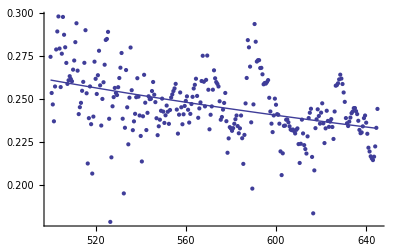

```mathematica
Show[ListPlot[f[2]], Plot[n[2][x], {x, 500, 645}]]
```

```mathematica
p[2]
```

| Estimate | Standard Error | Confidence Interval
a | 4.22344 | 1.4783 | {1.31385,7.13304}
b | -0.447885 | 0.0551836 | {-0.556498,-0.339272}

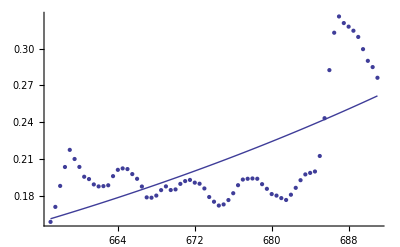

```mathematica
Show[ListPlot[f[3]], Plot[n[3][x], {x, 657, 691}]]
```

```mathematica
p[3]
```

| Estimate | Standard Error | Confidence Interval
a | 2.26717×10^-28 | 4.40665×10^-30 | {2.17921×10^-28,2.35513×10^-28}
b | 9.53063 | 6.5111×10^-57 | {9.53063,9.53063}

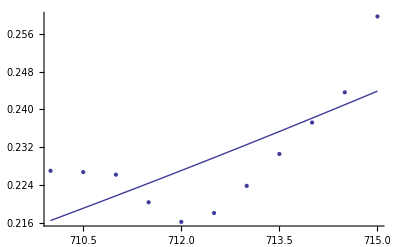

```mathematica
Show[ListPlot[f[4]], Plot[n[4][x], {x, 710, 715}]]
```

```mathematica
p[4]
```

| Estimate | Standard Error | Confidence Interval
a | 1.02148×10^-49 | 1.27351×10^-51 | {9.9267×10^-50,1.05029×10^-49}
b | 16.9491 | 8.54527×10^-100 | {16.9491,16.9491}

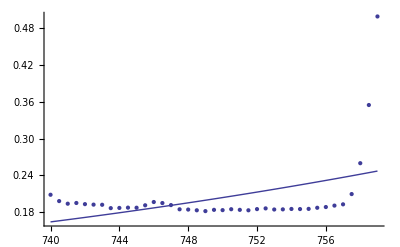

```mathematica
Show[ListPlot[f[5]], Plot[n[5][x], {x, 740, 759}]]
```

```mathematica
p[5]
```

| Estimate | Standard Error | Confidence Interval
a | 7.421×10^-48 | 3.05586×10^-49 | {6.80183×10^-48,8.04018×10^-48}
b | 16.1522 | 1.50152×10^-95 | {16.1522,16.1522}

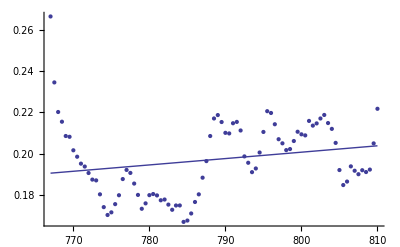

```mathematica
Show[ListPlot[f[6]], Plot[n[6][x], {x, 767, 810}]]
```

```mathematica
p[6]
```

| Estimate | Standard Error | Confidence Interval
a | 0.0000538788 | 0.000214995 | {-0.000373589,0.000481347}
b | 1.23019 | 0.598195 | {0.0408139,2.41956}

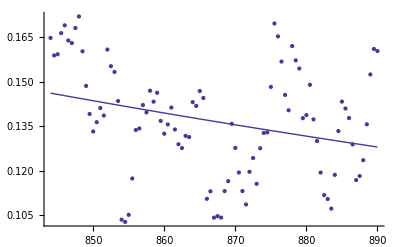

```mathematica
Show[ListPlot[f[7]], Plot[n[7][x], {x, 844, 890}]]
```

```mathematica
p[7]
```

| Estimate | Standard Error | Confidence Interval
a | 3.12232×10^6 | 1.84002×10^7 | {-3.34274×10^7,3.9672×10^7}
b | -2.50472 | 0.871281 | {-4.23541,-0.774025}

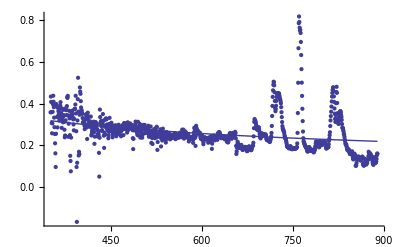

```mathematica
Show[ListPlot[f[22]], Plot[n[22][x], {x, 350, 890}]]
```

```mathematica
p[22]
```

| Estimate | Standard Error | Confidence Interval
a | 3.26501 | 0.761117 | {1.77158,4.75845}
b | -0.397431 | 0.0367396 | {-0.469521,-0.325342}

```mathematica
Array[c,3]
c[1]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-188-1051.IRR"]
c[2]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-200-1312.IRR"]
c[3]=Import["/net/home/f10/r1xu/Summer_Research/2010/C2010-208-1328.IRR"]
Array[nlm,3]
i=1;While[i<4,nlm[i]=NonlinearModelFit[c[i],a x^b,{a,b},x,MaxIterations->10000];i++]
Array[pwmo,3]
j=1;While[j<4,pwmo[j]=nlm[j]["ParameterConfidenceIntervalTable"];j++]
```

{{{368.,0.32149},{412.,0.33993},{500.,0.274642},{610.,0.223833},{675.,0.173321},{778.,0.185638},{862.,0.128747}},{{368.,0.103941},{412.,0.140975},{500.,0.125028},{610.,0.126214},{675.,0.104322},{778.,0.118859},{862.,0.0887751}},{{368.,0.307853},{412.,0.352929},{500.,0.291875},{610.,0.249881},{675.,0.211676},{778.,0.214968},{862.,0.187754}}}

{{368.,0.32149},{412.,0.33993},{500.,0.274642},{610.,0.223833},{675.,0.173321},{778.,0.185638},{862.,0.128747}}

{{368.,0.103941},{412.,0.140975},{500.,0.125028},{610.,0.126214},{675.,0.104322},{778.,0.118859},{862.,0.0887751}}

{{368.,0.307853},{412.,0.352929},{500.,0.291875},{610.,0.249881},{675.,0.211676},{778.,0.214968},{862.,0.187754}}

{FittedModel[111.776/x^0.976107],FittedModel[0.427889/x^0.206411],FittedModel[16.3049/x^0.654345]}

{ | Estimate | Standard Error | Confidence Interval
a | 111.776 | 95.8282 | {-134.559,358.11}
b | -0.976107 | 0.138395 | {-1.33186,-0.620351}, | Estimate | Standard Error | Confidence Interval
a | 0.427889 | 0.508037 | {-0.878061,1.73384}
b | -0.206411 | 0.187689 | {-0.688882,0.27606}, | Estimate | Standard Error | Confidence Interval
a | 16.3049 | 12.2645 | {-15.2221,47.8318}
b | -0.654345 | 0.120401 | {-0.963847,-0.344844}}